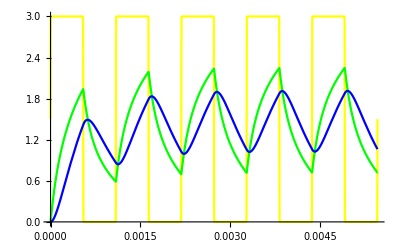

```mathematica
R1=10000;
R2=10000;
R3=1000000;
C1=33 * 10^-9;
C2=22*10^-9;
uZ[t]=amplituda*(1+Tanh[100*Sin[2*Pi*frekvence*t]])/2.2;

amplituda = 3.3;
frekvence = 917;

uzel1=iU[t]==iR1[t];
uzel2 = iR1[t] == iC1[t]+iR2[t];
uzel3 = iR2[t]==iC2[t]+iR3[t];

rovU=uZ[t]==u1[t];
rovR1 = u1[t]-u2[t]==R1*iR1[t];
rovR2=u2[t]-u3[t]==R2*iR2[t];
rovR3= u3[t]==R3*iR3[t];
rovC1 = iC1[t] ==C1*u2'[t];
rovC2 = iC2[t] == C2*u3'[t];

pp1= u2[0]==0;
pp2= u3[0]==0;

rovnice = {uzel1, uzel2,uzel3,rovU,rovR1, rovR2,rovR3,rovC1,rovC2, pp1,pp2};
nezname = {iU[t], iR1[t], iR2[t], iR3[t],iC1[t],iC2[t], u1[t],u2[t],u3[t]};

vysledek = NDSolve[rovnice, nezname,{t,0,5*frekvence^-1}, StartingStepSize->10^-9];
Plot[Evaluate[{u1[t], u2[t], u3[t]}/.vysledek], {t, 0, 5*frekvence^-1}, PlotStyle->{Yellow, Green, Blue}]
```